19/20

3

0

0.22

ⅇ^(3 x)

3 ⅇ^(3 x)

Riemann

-3^(19/20) ⅇ^(3 x) (-1+GammaRegularized[-19/20,3 x])

Caputo

-1/(x^(19/20) Gamma[1/20])-3^(19/20) ⅇ^(3 x) (-1+GammaRegularized[-19/20,3 x])

Liouville

Integrate::idiv: Integral of ⅇ^(3 xi)/(-x+xi)^(19/20) does not converge on {x,∞}.

Integrate[ⅇ^(3 xi)/(-x+xi)^(19/20),{xi,x,∞},Assumptions→x∈ℝ]/Gamma[1/20]

(∂_x Integrate[ⅇ^(3 xi)/(-x+xi)^(19/20),{xi,x,∞},Assumptions→x∈ℝ])/Gamma[1/20]

Liouville invert

Integrate::idiv: Integral of (3 ⅇ^(3 xi))/(-x+xi)^(19/20) does not converge on {x,∞}.

Integrate[(3 ⅇ^(3 xi))/(-x+xi)^(19/20),{xi,x,∞},Assumptions→x∈ℝ]/Gamma[1/20]

Feller

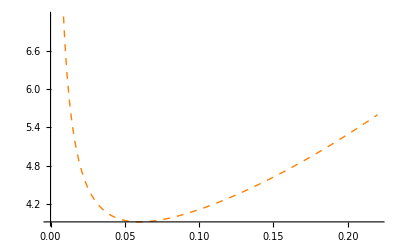

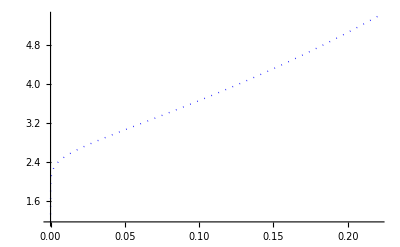

Integrate::idiv: Integral of ⅇ^(3 xi)/((-4.49429×10^-6+xi)^(19/20)) does not converge on {4.49429×10^-6,∞}.

General::ivar: 4.49429×10^-6 is not a valid variable.

NIntegrate::inumri: The integrand ⅇ^(3 xi)/((-4.49429×10^-6+xi)^(19/20)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{4.49429×10^-6,5.23043×10^7}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

General::ivar: 4.49429×10^-6 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

Integrate::idiv: Integral of ⅇ^(3 xi)/(-0.00449429+xi)^(19/20) does not converge on {0.00449429,∞}.

Integrate::idiv: Integral of ⅇ^(3 xi)/(-0.00898409+xi)^(19/20) does not converge on {0.00898409,∞}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

-Graphics-

Integrate::idiv: Integral of (3 ⅇ^(3 xi))/((-4.49429×10^-6+xi)^(19/20)) does not converge on {4.49429×10^-6,∞}.

NIntegrate::inumri: The integrand (3 ⅇ^(3 xi))/((-4.49429×10^-6+xi)^(19/20)) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{4.49429×10^-6,5.23043×10^7}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Integrate::idiv: Integral of (3 ⅇ^(3 xi))/(-0.00449429+xi)^(19/20) does not converge on {0.00449429,∞}.

Integrate::idiv: Integral of (3 ⅇ^(3 xi))/(-0.00898409+xi)^(19/20) does not converge on {0.00898409,∞}.

General::stop: Further output of Integrate::idiv will be suppressed during this calculation.

-Graphics-

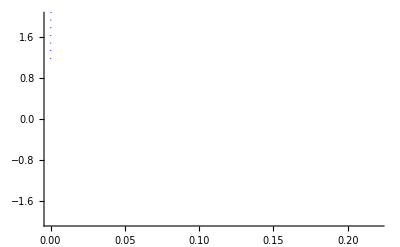

```mathematica
(*Input parameters*)
Clear[alpha,k,lb,ub]
alpha=95/100                             (*alpha*)
k=3                            (*k>0 in e^(k x)*)
lb=0                          (*plot lower bound*)
ub=0.22                         (*plot upper bound*)
(*Riemann official *)
fun[x_] = Exp[k x]
dfun[x_] = D[fun[x],x]
Print["Riemann"]
rieMat=FractionalD[fun[x],{x,alpha}]
(*Caputo official *)
Print["Caputo"]
capMat=CaputoD[fun[x],{x,alpha}]
(*Liouville *)
Print["Liouville"]
i1 = 1/Gamma[1-alpha]Integrate[(xi-x)^(-alpha)fun[xi],{xi,x,Infinity}, Assumptions->Element[x,Reals]]
lio = D[i1,x]
(*LiouvilleInvert *)
Print["Liouville invert"]
i2 = 1/Gamma[1-alpha]Integrate[(xi-x)^(-alpha)dfun[xi],{xi,x,Infinity}, Assumptions->Element[x,Reals]]

(*pot routines*)
pR1=Plot[rieMat,{x,lb,ub},PlotStyle->{Orange,Dashed,Thick}]
pC1=Plot[capMat,{x,lb,ub},PlotStyle->{Blue,Dotted,Thick},PlotRange->All]
pL1=Plot[lio       ,{x,lb,ub},PlotStyle->{Purple,Thick},PlotRange->All]
pL2=Plot[i2         ,{x,lb,ub},PlotStyle->{Green,Dashed},PlotRange->All]
(*errors:official versus derived in ex(3.4.2)*)

(*final output*)
Show[{pR1,pC1,pL1,pL2},PlotRange->{{lb,ub},{-2,2}}]
```